```mathematica
Clear["`*"]
```

### TreeForm

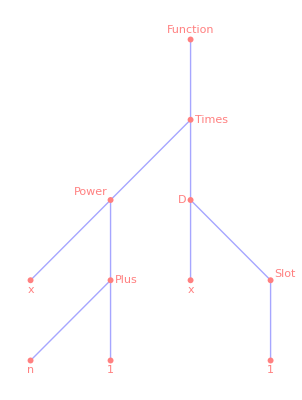

```mathematica
L[n_]:=(x^(n+1) D[#,x])&;
L[n]//TF[]//exportSVG["tree-example-Witt.svg"]
```

### Subexpressions

```mathematica
subexpr[expr_]:=
	Cases[expr,_,{0,Infinity}];
```

```mathematica
expr0=f[g[h]];
list=subexpr[expr0]
```

{h,g[h],f[g[h]]}

```mathematica
exprlist={a,b};
rulelist=Outer[Rule,list,exprlist]//Flatten
```

{h→a,h→b,g[h]→a,g[h]→b,f[g[h]]→a,f[g[h]]→b}

```mathematica
Map[
	Replace[expr0,#,{0,Infinity}]&,
	rulelist
]
```

{f[g[a]],f[g[b]],f[a],f[b],a,b}

```mathematica
Replace[expr0,g->a,{0,Infinity},Heads->False]
Replace[expr0,g->a,{0,Infinity},Heads->True]
```

f[g[h]]

f[a[h]]

```mathematica
Replace[expr0,f[g]->a,{0,Infinity},Heads->True]
Replace[expr0,f[g[x_]]:>a[x],{0,Infinity}]
```

f[g[h]]

a[h]

### Non-standard evaluation

```mathematica
f=g;
subexpr[f[1+1]]//Trace
```

{{{f,g},{1+1,2},g[2]},subexpr[g[2]],Cases[g[2],_,{0,∞}],{{∞,∞},{0,∞}},Cases[g[2],_,{0,∞}],{2,g[2]}}

```mathematica
subexpr2//Attributes=
	{HoldFirst};

subexpr2[expr_]:=
    Cases[Unevaluated@expr,
        subexpr_:>HoldForm@subexpr,
        {0,Infinity}
    ];
```

```mathematica
subexpr2[f[1+1]]
```

{1,1,1+1,f[1+1]}